## Телица Илья Денисович гр. 221701 Вариант 12

### Задание 1

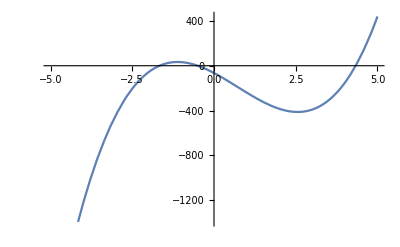

```mathematica
f[x_]=18*x^3-39*x^2-154*x-65;
Plot[f[x],{x,-5,5},AxesOrigin->{0,0}]
```

Решение с точностью ϵ:-1.66668 получено на 4 шаге.

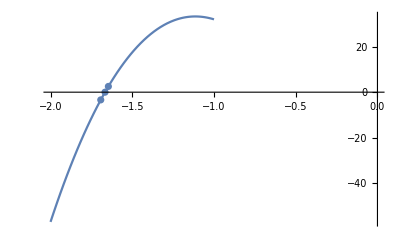

```mathematica
L=-2;R=5;ϵ=10^-3;
X=R-(f[R]*(R-L))/(f[R]-f[L]);
iter=0;
A={0,0,0};
(*Задание опорных значений*)
While[Abs[X-R]>ϵ,L=R;
R=X;X=R-(f[R]*(R-L))/(f[R]-f[L]);
iter++;If[iter<3,A[[iter]]=X]]
(*Использовании цикла для нахождения прилежения с требуемой точностью*) 
A[[3]]=X//N;
B=Table[{A[[i]],f[A[[i]]]},{i,1,3}];
Print["Решение с точностью ϵ:",X//N," получено на ",iter," шаге."];
Show[Plot[f[x],{x,-2,-1},AxesOrigin->{0,0}],ListPlot[B]]
(*Вывод найденого приближением корня и первых двух приближенных корней на графике*)
```

### Задание 2

```mathematica
f[x_]=x^6-6*x^5-24*x^4+82*x^3+315*x^2+324*x+108;
Echo[Solve[f[x]==0],"Нахождение корня методом Solve:"];
Echo[NSolve[f[x]==0],"Нахождение корня методом NSolve:"];
Echo[Roots[f[x]==0,x],"Нахождение корня методом Roots:"];
Echo[FindRoot[f[x]==0,{x,0}],"Нахождение корня ипользуя метод FindRoot:"];
Echo[Factor[f[x]],"Разложение многочлена на множители используя функцию Factor:"];
```

Нахождение корня метод Solve:  {{x→-3},{x→-1},{x→-1},{x→-1},{x→6},{x→6}}

Нахождение корня метод NSolve:  {{x→-3.},{x→-1.},{x→-1.},{x→-1.},{x→6.},{x→6.}}

Нахождение корня метод Roots:  x==-3||x==-1||x==-1||x==-1||x==6||x==6

Нахождение корня ипользуя метод FindRoot:  {x→-0.999996}

Разложение многочлена на множители используя функцию Factor:  (-6+x)^2 (1+x)^3 (3+x)

### Задание 3

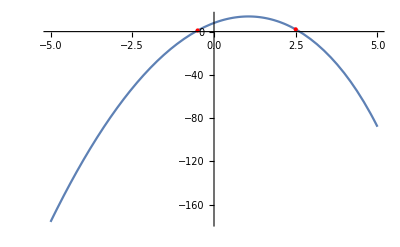

```mathematica
f[x_]=12*x-5 x^2-2^x+9;
f1[x_]=12*x-5*x^2;
f2[x_]=2^x-9;
Plot[f[x],{x,-5,5},Epilog->{Red,Point[{-0.5,f[-0.5]}],Point[{2.5,f[2.5]}]}]

(*Вывод графика трансцендентного уравнения и точек близких к корням уравнения*)
```

## Нахождение корня методом Ньютона :

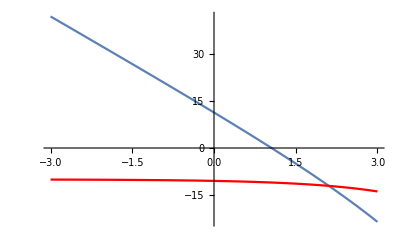

Решение x=-0.562032 получено на 3 шаге.

```mathematica
l[x_]=D[f[x],x];
l2[x_]=D[f[x],{x,2}];
gr1=Plot[l[x],{x,-3,3}];
gr2=Plot[l1[x],{x,-3,3}, PlotStyle->Red];
Show[gr1,gr2]
a=-0.8;b=-0.4;ϵ=10^-3;
x1=a;
(*Вторая производная < 0 поэтому берем левый отрицательный конец*)
Do[x2=x1;
x1=(x1-f[x1]/l[x1]);
If[Abs[x2-x1]<ϵ,
Print["Решение x=",x2//N," получено на ",n," шаге."];Break[]],
{n,1,100}]
```

## Нахождение корня методом секущих :

```mathematica
x2=b;x1=b-0.001;
Do[xn=x2;
x2=(x2-f[x2]/((f[x2]-f[x1])/(x2-x1)));
x1=xn;
If[Abs[x2-x1]<ϵ,
Print["Решение x=",x2//N," получено на ",n," шаге."];Break[]],
{n,1,100}]
```

Решение x=-0.561965 получено на 3 шаге.

### Задание 4

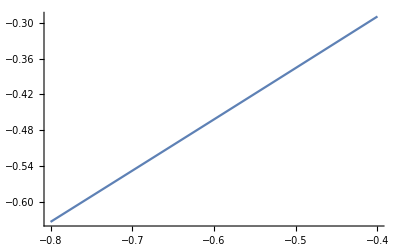

Решение x=-0.562344 получено на 8 шаге.

```mathematica
f[x_]=12*x-5 x^2-2^x+9;
fi[x_]=(5*x^2+2^x-9)/12;
(*Способ выражения переменной Х через оставшиеся переменные*)
l3[x_]=D[fi[x],x];
Plot[l3[x],{x,a,b}]
(*Проверка достаточного условия сходимости итерационного процесса для выбранной функции*)
x1=b;
Do[x2=x1;
x1=fi[x1]//N;
If[Abs[x2-x1]<ϵ,
Print["Решение x=",x2//N," получено на ",n," шаге."];Break[]],
{n,1,100}]
```

### Задание 5

```mathematica
Echo[Solve[12*x-5 x^2-2^x+9==0,Reals],"Нахождение корня методом Solve:"];
Echo[NSolve[12*x-5 x^2-2^x+9==0,Reals],"Нахождение корня методом NSolve:"];
Echo[FindRoot[12*x-5 x^2-2^x+9==0,{x,-0.8}],"Нахождение корня методом FindRoot:"];
```

Нахождение корня методом Solve:  {{x→Root-0.562Root[{-9+2^#1-12 #1+5 #1^2&,-0.56196603626120455608}]-0.5619660362612046},{x→Root2.62Root[{-9+2^#1-12 #1+5 #1^2&,2.6184011112622617823}]2.6184011112622616}}

Нахождение корня методом NSolve:  {{x→-0.561966},{x→2.6184}}

Нахождение корня методом FindRoot:  {x→-0.561966}

### Задание 6

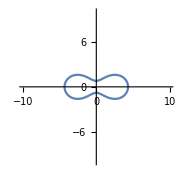

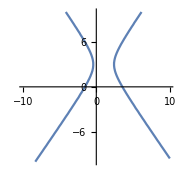

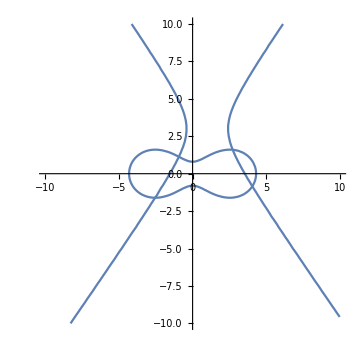

{x→-0.93492,y→1.13243}

{x→-2.5515,y→-1.6072}

{x→2.72677,y→1.59876}

{x→4.06273,y→-0.841952}

```mathematica
f[x_,y_]=(x^2+y^2)^2-18*(x^2-y^2)-12;
g[x_,y_]=2*x^2-y^2-4*x+6*y-11;
gr1=ContourPlot[f[x,y]==0,{x,-10,10},{y,-10,10},Axes->True,Frame->False, ImageSize->Small]
(*Первый график*)
gr2=ContourPlot[g[x,y]==0,{x,-10,10},{y,-10,10},Axes->True,Frame->False, ImageSize->Small]
(*Второй график*)
Show[gr1,gr2,ImageSize->Medium]
(*Графики вместе*)
FindRoot[{f[x,y]==0,g[x,y]==0},{x,-1},{y,1}]
FindRoot[{f[x,y]==0,g[x,y]==0},{x,-2.5},{y,-1.7}]
FindRoot[{f[x,y]==0,g[x,y]==0},{x,3},{y,1.5}]
FindRoot[{f[x,y]==0,g[x,y]==0},{x,4},{y,-1}]
(*Поиск корней используя точки пересечения как начальное приближение*)
```